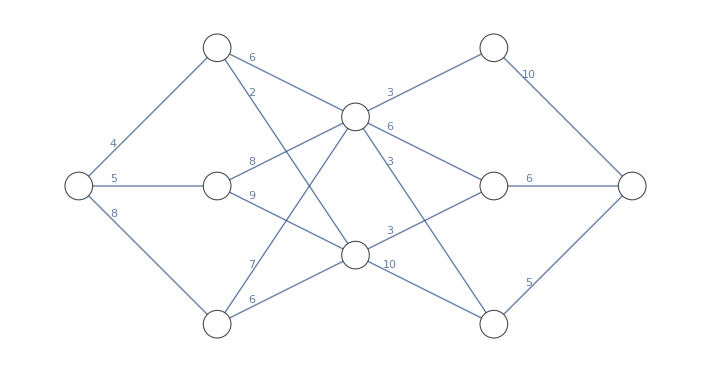

```mathematica
nodes={"A","B1","B2","B3","C1","C2","D1","D2","D3","E"};(*定义所有的点*)
edgesWithValues={"A"<->"B1"->Placed[4,1/4],"A"<->"B2"->Placed[5,1/4],"A"<->"B3"->Placed[8,1/4],"B1"<->"C1"->Placed[6,1/4],"B1"<->"C2"->Placed[2,1/4],"B2"<->"C1"->Placed[8,1/4],"B2"<->"C2"->Placed[9,1/4],"B3"<->"C1"->Placed[7,1/4],"B3"<->"C2"->Placed[6,1/4],"C1"<->"D1"->Placed[3,1/4],"C1"<->"D2"->Placed[6,1/4],"C1"<->"D3"->Placed[3,1/4],"C2"<->"D2"->Placed[3,1/4],"C2"<->"D3"->Placed[10,1/4],"D1"<->"E"->Placed[10,1/4],"D2"<->"E"->Placed[6,1/4],"D3"<->"E"->Placed[5,1/4]};(*定义所有的边的数值和位置*)
edges=edgesWithValues[[All,1]]/.Rule->UndirectedEdge;
graph=Graph[nodes,edges,EdgeLabels->edgesWithValues,VertexLabels->Placed[Automatic,Center],VertexStyle->Hue[0.62,0,1],GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->"A","Orientation"->Left},VertexSize->0.2];
adjustedPositions=AssociationThread[nodes,{{0,3},{2,5},{2,3},{2,1},{4,4},{4,2},{6,5},{6,3},{6,1},{8,3}}];(*利用坐标网格确定各个顶点的位置*)
SetProperty[graph,VertexCoordinates->Normal[adjustedPositions]](*应用图形结果*)
```